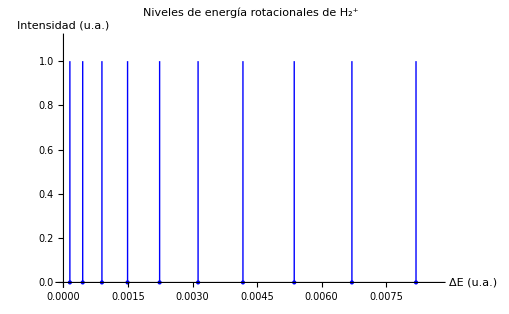

```mathematica
(*Constantes en unidades atómicas*)
mu=918;
Xmin=2.70359;
(*Energía rotacional en Hartree*)
Erot[j_]:=(j*(j+1))/(2*mu*Xmin^2);

(*Diferencias de energía respecto a J=0*)
Jmax=10;
linePositions=Table[Erot[j]-Erot[0],{j,1,Jmax}];
(*Construir puntos en el eje x para fijar el rango*)
points=Table[{pos,0},{pos,linePositions}]; (*"pos" representa las posiciones de las líneas espectrales en el eje horizontal (energía).*)
(*Construir líneas verticales desde 0 hasta 1*)
lines=Table[Line[{{pos,0},{pos,1}}],{pos,linePositions}];
(*Graficar*)
Show[ListPlot[points,PlotStyle->{Blue,PointSize[Medium]}],Graphics[{Blue,lines}],Axes->True,AxesLabel->{"ΔE (u.a.)","Intensidad (u.a.)"},PlotRange->{{0,Max[linePositions]+0.0005},{0,1.1}},PlotLabel->"Niveles de energía rotacionales de H₂⁺"]
```

```mathematica
(* convertir a E=hc/λ, otra gráfica: 1/λ*)
```